```mathematica
SL=Solve[x^6-21 x^5+175 x^4-735 x^3+1624 x^2-1764x+720==0]
```

{{x→1},{x→2},{x→3},{x→4},{x→5},{x→6}}

```mathematica
Sum[SL[[k,1,2]]^2,{k,1,6}]
```

91

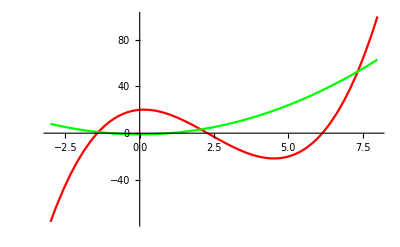

```mathematica
f[x_]=x^3-7x^2+2*x+20;
g[x_]=x^2-1;
Plot[{f[x],g[x]},{x,-3,8},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
```

```mathematica
Solve[f[x]==g[x],x]
```

{{x→1/3 (8+58/(1/2 (313+3 ⅈ √75831))^(1/3)+(1/2 (313+3 ⅈ √75831))^(1/3))},{x→8/3-(29 (1+ⅈ √3))/(3 (1/2 (313+3 ⅈ √75831))^(1/3))-1/6 (1-ⅈ √3) (1/2 (313+3 ⅈ √75831))^(1/3)},{x→8/3-(29 (1-ⅈ √3))/(3 (1/2 (313+3 ⅈ √75831))^(1/3))-1/6 (1+ⅈ √3) (1/2 (313+3 ⅈ √75831))^(1/3)}}

```mathematica
%//N
```

{{x→7.33735-2.96059×10^-16 ⅈ},{x→-1.39258+2.22045×10^-16 ⅈ},{x→2.05523+0. ⅈ}}

```mathematica
f[x_]=x^5-20 x^4-16 x^3+16 x^2-22x-12;
Subscript[a, n]=1;
Subscript[a, n-1]=-20;
Subscript[a, 0]=-12;
sol=NSolve[f[x]==0,x]
```

{{x→-1.51779},{x→-0.403707},{x→0.592302-0.770444 ⅈ},{x→0.592302+0.770444 ⅈ},{x→20.7369}}

```mathematica
Sum[sol[[k,1,2]],{k,1,5}]==-Subscript[a, n-1]/Subscript[a, n]
```

True

```mathematica
Product[sol[[k,1,2]],{k,1,5}]==(-1)^5->*Subscript[a, 0]/Subscript[a, n]
```

False

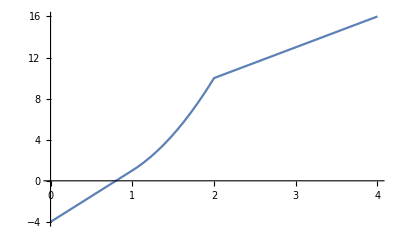

```mathematica
f[x_]:=5*x-4/;0<x≤1
f[x_]:=4*x^2-3*x/;1<x<2
f[x_]:=3*x+4/;2≤x
Plot[f[x],{x,0,4}]
RHL=Limit[f[x],x->0,Direction->-1];
LHL=Limit[f[x],x->0,Direction->1];
F0=1;
If[LHL==F0==RHL,Print["f is continuous"],Print["f is not continuous"]]
```

```mathematica
f[x_]:=5*x-4/;0<x≤1
f[x_]:=4*x^2-3*x/;1<x<2
f[x_]:=3*x+4/;2≤x
Plot[f[x],{x,0,4}]
```

-Graphics-

```mathematica
LHD=Limit[(f[1+h]-f[1])/h,h->0,Direction->1]/.x->1
LHD=Limit[(f[1+h]-f[1])/h,h->0,Direction->-1]/.x->1
LHD==Rh
```